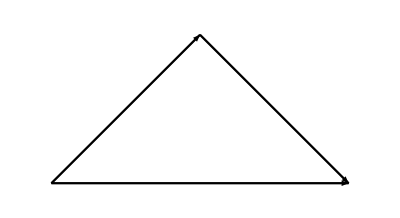

```mathematica
Quxian1=Plot[x,{x,0,1},PlotStyle->Black];
Quxian2=Plot[2-x,{x,1,2},PlotStyle->Black];
Quxian3=Plot[0,{x,0,2},PlotStyle->Black];
g1=Graphics[{Arrowheads[0.05],Arrow[{{0,0},{1,1}}]}];
g2=Graphics[{Arrowheads[0.05],Arrow[{{1,1},{2,0}}]}];
g3=Graphics[{Arrowheads[0.05],Arrow[{{0,0},{2,0}}]}];
Show[Quxian1,Quxian2,Quxian3,g1,g2,g3,PlotRange->{{-0.1,2.1},{-0.1,1.1}},AxesStyle->Arrowheads[0.04],Axes->Automatic,AspectRatio->1.2/2.2,Frame->False,Ticks->{{1,2},{1}}]
```

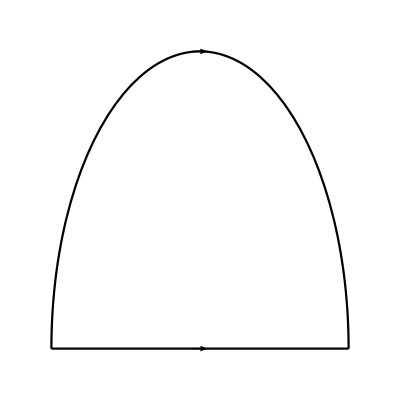

```mathematica
P1=ParametricPlot[{Cos[t],2Sin[t]},{t,0,Pi},PlotStyle->Black];
P2=Plot[0,{t,-1,1},PlotStyle->Black];
g1=Graphics[{Arrowheads[0.05],Arrow[{{0-0.05,2},{0+0.05,2}}]}];
g2=Graphics[{Arrowheads[0.05],Arrow[{{0-0.05,0},{0+0.05,0}}]}];
Show[P1,P2,g1,g2,PlotRange->{{-1.1,1.1},{-0.1,2.1}},AxesStyle->Arrowheads[0.04],Axes->Automatic,AspectRatio->2.2/2.2,Frame->False,Ticks->{{-1,1},{2}}]
```

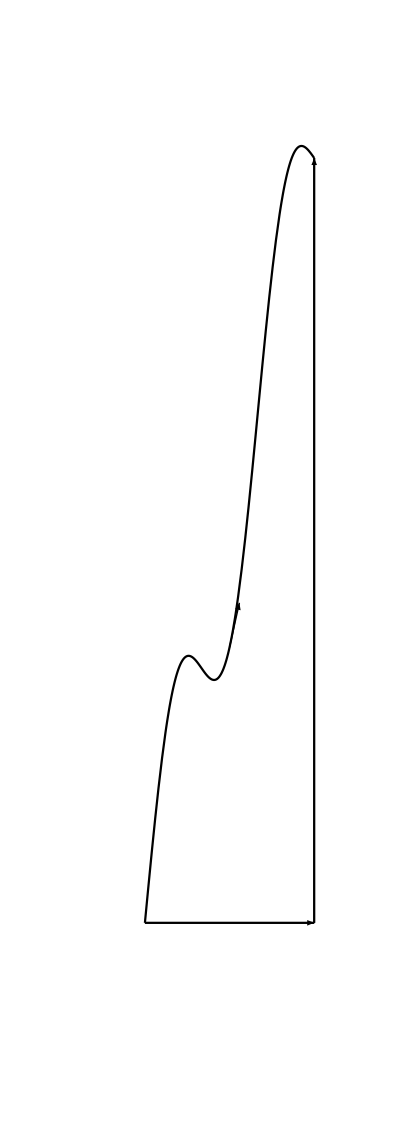

```mathematica
F[x_]=(Sin[3Pi/(E-1)(x-1)])+((3E-1)/(E-1)(x-1)+1);
DF[x_]=F'[x];
P1=Plot[F[x],{x,1,E},PlotStyle->Black];
P2=Plot[1,{x,1,E},PlotStyle->Black];
P3=ParametricPlot[{E,y},{y,1,3E},PlotStyle->Black];
g1=Graphics[{Arrowheads[0.125],Arrow[{{1,1},{E,1}}]}];
g2=Graphics[{Arrowheads[0.125],Arrow[{{E,1},{E,3E}}]}];
g3=Graphics[{Arrowheads[0.125],Arrow[{{(E+1)/2,F[(E+1)/2]},{(E+1)/2+0.1,F[(E+1)/2]+0.1*DF[(E+1)/2]}}]}];
Show[P1,P2,P3,g1,g2,g3,PlotRange->{{-0.1,E+0.5},{-0.1,3E+0.5}},AxesStyle->Arrowheads[0.08],Axes->Automatic,AspectRatio->(3E+0.2)/(E+0.2),Frame->False,Ticks->{{0,1,E},{1,3E}},AxesOrigin->{0,0}]
```

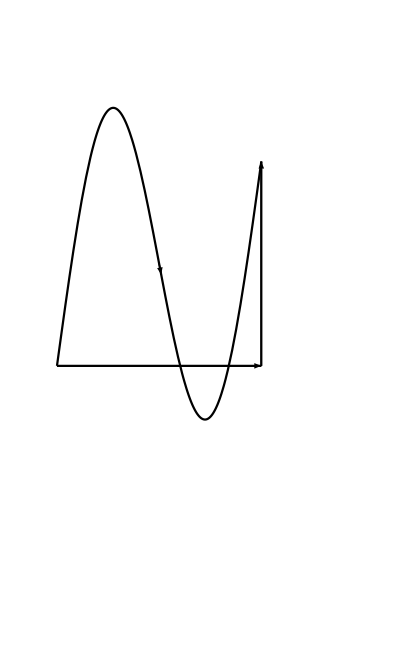

```mathematica
F[x_]=(Sin[2Pi/(1-0)(x-0)])+((2-1)/(1-0)(x-0)+1);
DF[x_]=F'[x];
P1=Plot[F[x],{x,0,1},PlotStyle->Black];
P2=Plot[1,{x,0,1},PlotStyle->Black];
P3=ParametricPlot[{1,y},{y,1,2},PlotStyle->Black];
g1=Graphics[{Arrowheads[0.08],Arrow[{{0,1},{1,1}}]}];
g2=Graphics[{Arrowheads[0.08],Arrow[{{1,1},{1,2}}]}];
g3=Graphics[{Arrowheads[0.08],Arrow[{{(1+0)/2,F[(1+0)/2]},{(1+0)/2+0.01,F[(1+0)/2]+0.01*DF[(1+0)/2]}}]}];
Show[P1,P2,P3,g1,g2,g3,PlotRange->{{-0.1,1+0.5},{-0.1,2+0.5}},AxesStyle->Arrowheads[0.06],Axes->Automatic,AspectRatio->(2+0.6)/(1+0.6),Frame->False,Ticks->{{0,1,E},{1,3E}},AxesOrigin->{0,0}]
```

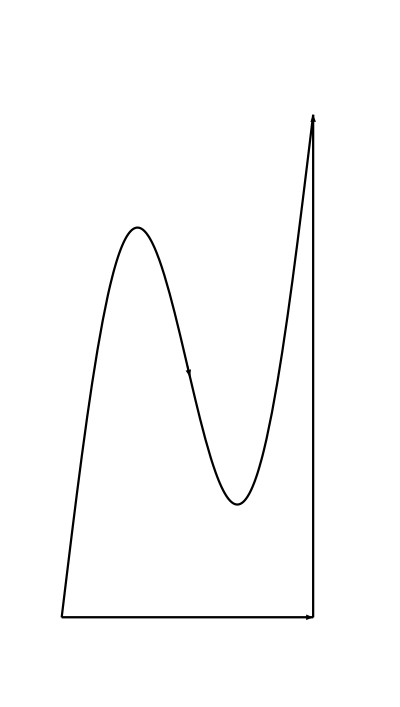

```mathematica
F[x_]=(Sin[2Pi/(1-0)(x-0)])+((2-0)/(1-0)(x-0));
DF[x_]=F'[x];
P1=Plot[F[x],{x,0,1},PlotStyle->Black];
P2=Plot[0,{x,0,1},PlotStyle->Black];
P3=ParametricPlot[{1,y},{y,0,2},PlotStyle->Black];
g1=Graphics[{Arrowheads[0.08],Arrow[{{0,0},{1,0}}]}];
g2=Graphics[{Arrowheads[0.08],Arrow[{{1,0},{1,2}}]}];
g3=Graphics[{Arrowheads[0.08],Arrow[{{(1+0)/2,F[(1+0)/2]},{(1+0)/2+0.01,F[(1+0)/2]+0.01*DF[(1+0)/2]}}]}];
Show[P1,P2,P3,g1,g2,g3,PlotRange->{{-0.1,1+0.2},{-0.1,2+0.2}},AxesStyle->Arrowheads[0.06],Axes->Automatic,AspectRatio->(2+0.3)/(1+0.3),Frame->False,Ticks->{{0,1,E},{1,3E}},AxesOrigin->{0,0}]
```

```mathematica
Fx[phi_,theta_]=1.0Sin[phi]Cos[theta]+0.1;
Fy[phi_,theta_]=0.9 Sin[phi]Sin[theta]+0.1;
Fz[phi_,theta_]=0.8Cos[phi]+0.1;
DFxu[phi_,theta_]=D[Fx[phi,theta],phi];
DFxv[phi_,theta_]=D[Fx[phi,theta],theta];
DFyu[phi_,theta_]=D[Fy[phi,theta],phi];
DFyv[phi_,theta_]=D[Fy[phi,theta],theta];
DFzu[phi_,theta_]=D[Fz[phi,theta],phi];
DFzv[phi_,theta_]=D[Fz[phi,theta],theta];
vx[x_,y_,z_]=x/Sqrt[x^2+y^2+z^2];
vy[x_,y_,z_]=y/Sqrt[x^2+y^2+z^2];
vz[x_,y_,z_]=z/Sqrt[x^2+y^2+z^2];
v[phi_,theta_]={vx[Fx[phi,theta],Fy[phi,theta],Fz[phi,theta]],vy[Fx[phi,theta],Fy[phi,theta],Fz[phi,theta]],vz[Fx[phi,theta],Fy[phi,theta],Fz[phi,theta]]};
PLTP=10;
nn=Cross[{DFxu[Pi/4,Pi/4],DFyu[Pi/4,Pi/4],DFzu[Pi/4,Pi/4]},{DFxv[Pi/4,Pi/4],DFyv[Pi/4,Pi/4],DFzv[Pi/4,Pi/4]}];
P1=ParametricPlot3D[{Fx[phi,theta],Fy[phi,theta],Fz[phi,theta]},{phi,0,Pi},{theta,0,2Pi},Axes->False, BoxRatios->{1,1,1},PlotStyle->{Blue,Opacity[0.5]},Mesh->0,PlotPoints->PLTP];
P3=ParametricPlot3D[{Fx[phi,theta],Fy[phi,theta],Fz[phi,theta]},{phi,Pi/4-Pi/20,Pi/4+Pi/20},{theta,Pi/4-Pi/20,Pi/4+Pi/20},Axes->False, BoxRatios->{1,1,1},PlotStyle->{Blue,Opacity[0.6]},Mesh->0,PlotPoints->PLTP];
P4=ParametricPlot3D[{Fx[phi,theta],Fy[phi,theta],Fz[phi,theta]}+v[Pi/4,Pi/4],{phi,Pi/4-Pi/20,Pi/4+Pi/20},{theta,Pi/4-Pi/20,Pi/4+Pi/20},Axes->False, BoxRatios->{1,1,1},PlotStyle->{Black,Opacity[0.6]},Mesh->0,PlotPoints->PLTP];
P5=ParametricPlot3D[{Fx[phi,Pi/4-Pi/20],Fy[phi,Pi/4-Pi/20],Fz[phi,Pi/4-Pi/20]}+h v[Pi/4,Pi/4],{phi,Pi/4-Pi/20,Pi/4+Pi/20},{h,0,1},Axes->False, BoxRatios->{1,1,1},PlotStyle->{Green,Opacity[0.6]},Mesh->0,PlotPoints->PLTP];
P6=ParametricPlot3D[{Fx[phi,Pi/4+Pi/20],Fy[phi,Pi/4+Pi/20],Fz[phi,Pi/4+Pi/20]}+h v[Pi/4,Pi/4],{phi,Pi/4-Pi/20,Pi/4+Pi/20},{h,0,1},Axes->False, BoxRatios->{1,1,1},PlotStyle->{Green,Opacity[0.6]},Mesh->0,PlotPoints->PLTP];
P7=ParametricPlot3D[{Fx[Pi/4+Pi/20,theta],Fy[Pi/4+Pi/20,theta],Fz[Pi/4+Pi/20,theta]}+h v[Pi/4,Pi/4],{theta,Pi/4-Pi/20,Pi/4+Pi/20},{h,0,1},Axes->False, BoxRatios->{1,1,1},PlotStyle->{Green,Opacity[0.6]},Mesh->0,PlotPoints->PLTP];
P8=ParametricPlot3D[{Fx[Pi/4-Pi/20,theta],Fy[Pi/4-Pi/20,theta],Fz[Pi/4-Pi/20,theta]}+h v[Pi/4,Pi/4],{theta,Pi/4-Pi/20,Pi/4+Pi/20},{h,0,1},Axes->False, BoxRatios->{1,1,1},PlotStyle->{Green,Opacity[0.6]},Mesh->0,PlotPoints->PLTP];
P9=ParametricPlot3D[{Fx[Pi/4,Pi/4],Fy[Pi/4,Pi/4],Fz[Pi/4,Pi/4]}+v[Pi/4,Pi/4]-h(v[Pi/4,Pi/4]-(v[Pi/4,Pi/4].Normalize[nn])Normalize[nn]),{h,0,1},Axes->False, BoxRatios->{1,1,1},PlotStyle->{Green,Opacity[1],Dashing[{0.01,0.005}]},Mesh->0,PlotPoints->PLTP];
g1=Graphics3D[{Blue,Arrowheads[0.02],Arrow[{{Fx[Pi/4,Pi/4],Fy[Pi/4,Pi/4],Fz[Pi/4,Pi/4]},{Fx[Pi/4,Pi/4],Fy[Pi/4,Pi/4],Fz[Pi/4,Pi/4]}+Normalize[nn]}]}];
g2=Graphics3D[{Red,Arrowheads[0.02],Arrow[{{0.1,0.1,0.1},{0.1*2,0.1*2,0.1*2}}]}];
g3=Graphics3D[{Black,Arrowheads[0.02],Arrow[{{Fx[Pi/4,Pi/4],Fy[Pi/4,Pi/4],Fz[Pi/4,Pi/4]},{Fx[Pi/4,Pi/4],Fy[Pi/4,Pi/4],Fz[Pi/4,Pi/4]}+v[Pi/4,Pi/4]}]}];

G1=Graphics3D[{{Black,Arrowheads[.03],Arrow[{{-1.4,0,0},{1.6,0,0}}]},{Black,Arrowheads[.03],Arrow[{{0,0,-1.2},{0,0,1.4}}]},{Black,Arrowheads[.03],Arrow[{{0,-1.3,0},{0,1.5,0}}]}},Axes->False,AxesOrigin->{0,0,0}];
Show[G1,P1,P3,P4,P5,P6,P7,P8,P9,g1,g3,ViewPoint->{6,-2,2},Boxed->False,AxesOrigin->{0,0,0}]
```

-Graphics3D-

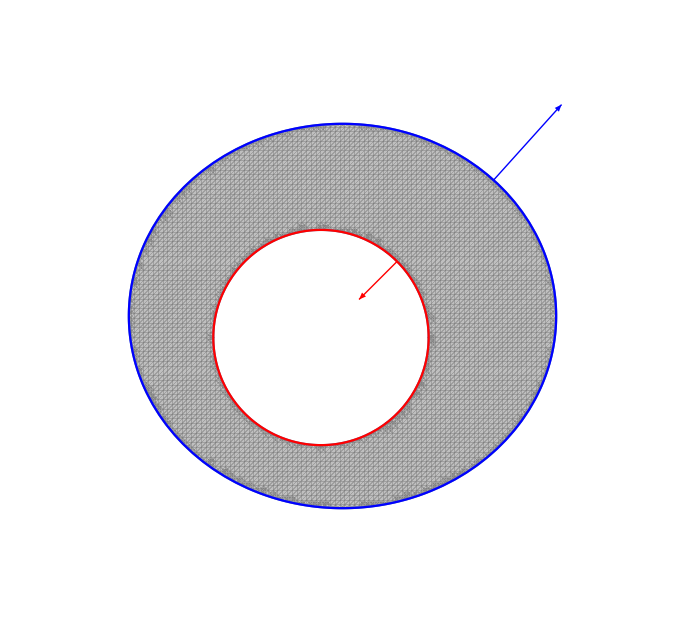

```mathematica
Fx[phi_,theta_]=1.0Sin[phi]Cos[theta]+0.1;
Fy[phi_,theta_]=0.9 Sin[phi]Sin[theta]+0.1;
DFxv[phi_,theta_]=D[Fx[phi,theta],theta];
DFyv[phi_,theta_]=D[Fy[phi,theta],theta];
PLTP=100;
rx[theta_]=0.5Cos[theta];
ry[theta_]=0.5Sin[theta];
Drx[theta_]=rx'[theta];
Dry[theta_]=ry'[theta];
P1=ParametricPlot[{Fx[ArcCos[-1/8],theta],Fy[ArcCos[-1/8],theta]},{theta,0,2Pi},Axes->False,PlotStyle->{Blue},Mesh->0,PlotPoints->PLTP];
P2=ParametricPlot[{0.5Cos[theta],0.5Sin[theta]},{theta,0,2Pi},Axes->False,PlotStyle->{Red},Mesh->0,PlotPoints->PLTP];
P4=RegionPlot[x^2+y^2>0.25&&((x-0.1)/Sin[ArcCos[-1/8]])^2+((y-0.1)/0.9/Sin[ArcCos[-1/8]])^2<1,{x,-1,1.2},{y,-1,1.2},Axes->False,PlotStyle->{Gray,Opacity[0.5]},Mesh->0,PlotPoints->PLTP];
P3=RegionPlot[x^2+y^2<0.25,{x,-1,1.2},{y,-1,1.2},Axes->False,PlotStyle->{Gray,Opacity[0.5]},Mesh->0,PlotPoints->PLTP];
g1=Graphics[{Red,Arrowheads[0.04],Arrow[{{rx[Pi/4],ry[Pi/4]},{rx[Pi/4],ry[Pi/4]}+0.5{-Dry[Pi/4],Drx[Pi/4]}}]}];
g2=Graphics[{Blue,Arrowheads[0.04],Arrow[{{Fx[ArcCos[-1/8],Pi/4],Fy[ArcCos[-1/8],Pi/4]},{Fx[ArcCos[-1/8],Pi/4],Fy[ArcCos[-1/8],Pi/4]}-0.5{-DFyv[ArcCos[-1/8],Pi/4],DFxv[ArcCos[-1/8],Pi/4]}}]}];
Show[P4,P1,P2,g1,g2,PlotRange->{{-1.2,1.4},{-1.1,1.3}},AxesStyle->Arrowheads[0.06],Axes->Automatic,AspectRatio->2.4/2.6,Frame->False,Ticks->None,AxesOrigin->{0,0}]
```